## Parameters

```mathematica
wd=NotebookDirectory[];
SetDirectory[wd];
(*Read parameter file into conf*)
readConf[filename_]:=Module[{res={},i,rawF,Ln,chk},
rawF=ReadList[filename,"String"];
Print[Length[rawF]];
For[i=1,i<=Length[rawF],++i,
If[rawF[[i]]=={},Continue[]];
If[StringTake[rawF[[i]],1]=="#",Continue[]];
Ln=StringSplit[rawF[[i]]];
If[NumericQ[ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->ToExpression[Ln[[2]]]],AppendTo[res,Ln[[1]]->Ln[[2]]]];
];
Association[res]
];
(*Parameters can be called same as in py*)
conf=readConf["../params"];
StateList={"1S"};
```

68

```mathematica
conf
```

<|L→50,dt→0.1,T→0.3,tFn→1500,NY→2000,Nbb→0,ECut→20,prCut→12,NPts→100,ExportRates→True,NXPart→16,NThreads→14,HydroMode→0,HPts→20,Mb→4.65,M1S→9.46,M2S→10.023,E1S→0.13,E2S→0.723,bsig→0.01,Ysig→0.02,alphaS→0.3,CF→1.3333333333333333333,NC→3,gs→0.75,Ch→0,rateFile→bottom_rates_2d.tsv,boop→gleep|>

### Matrix Elements

```mathematica
aB[st_]:=2/(conf["alphaS"]*conf["CF"]*conf["M"<>st]);
(*Matrix Elements*)
MOvLp[prel_,st_]:=Piecewise[{{
(((2^10)(Pi)(aB[st]^7)(prel^2)))/((1+(aB[st]^2)(prel^2))^6),st=="1S"},
{
((2^21)(Pi)(aB[st]^7)(prel^2)(1-2(aB[st]^2)(prel^2))^2)/((1+4(aB[st]^2)(prel^2))^8),st=="2S"}}];
```

```mathematica
fB[p_,M_,T_]:=p^2Exp[-Sqrt[M^2+p^2]/T];
```

## Dissociation Channels

### Real Gluon Absorption

```mathematica
(* RGA rate *)
ΓRGAint[st_,q_,γ_]:=(2*conf["alphaS"]*conf["M"<>st]*conf["T"]/(9(Pi^2)(γ^2)*Sqrt[1-(1/γ^2)]))*(q^2)Sqrt[conf["M"<>st](q-conf["E"<>st])]Log[((1-Exp[-γ(1+Sqrt[1-(1/γ^2)])q/conf["T"]])/(1-Exp[-γ(1-Sqrt[1-(1/γ^2)])q/conf["T"]]))]*MOvLp[Sqrt[conf["M"<>st](q-conf["E"<>st])],st];
(* Integrate out q for (directly)sampled p-points~γ-points *)
ΓRGA1S=Table[{p,NIntegrate[ΓRGAint["1S",q,1/Sqrt[1-(p/Sqrt[p^2+conf["M"<>"1S"]^2])^2]],{q,conf["E"<>"1S"],Infinity}]},{p,0.1,conf["prCut"],0.01}];
```

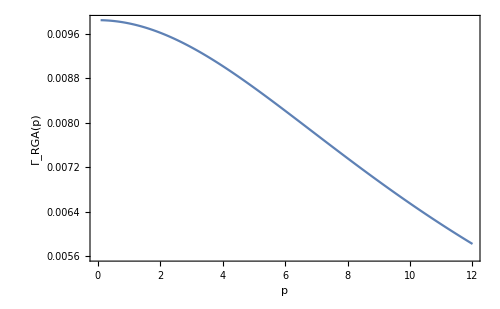

```mathematica
ListPlot[ΓRGA1S,Joined->True,PlotRange->All,Frame->True,FrameLabel->{{"Γ_RGA(p)",""},{"p","RGA marginal rate"}},FrameStyle->Directive[Black,FontSize->12],ImageSize->500]
```

```mathematica
(*Sample Dissociation Approximation (1S)*)
```

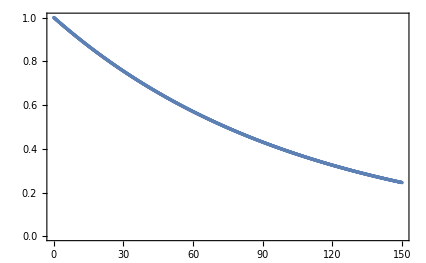

```mathematica
RGAsampLF={{0,1}};
RGAsampDist=(1)(1/NIntegrate[fB[p,conf["M1S"],conf["T"]],{p,0,Infinity}])*Table[fB[pi,conf["M1S"],conf["T"]],{pi,0,conf["prCut"],0.1}];
RGAsampInterp=Interpolation[ΓRGA1S];
ΓRGAresamp=RGAsampInterp/@Table[pi,{pi,0,conf["prCut"],0.1}]//Quiet;
(*Iterate application of += -(Ni*fB[p]*ΓRGA[p])*)
For[i=1,i<=conf["tFn"],++i,
RGAsampDist=RGAsampDist-(RGAsampDist*ΓRGAresamp*conf["dt"]);
AppendTo[RGAsampLF,{i*conf["dt"],Total[RGAsampDist]*(conf["prCut"]/(Length[RGAsampDist]-1))}];
];
ListPlot[RGAsampLF,Frame->True]
```

## Recombination Channels

## Equilibrium Values

```mathematica
frel[T_,M_,g_]:=g*(conf["L"]^3)*(1/(2*Pi^2))*(M^2)*T*BesselK[2,M/T];
fnon[T_,M_,g_]:=g*(conf["L"]^3)*(M*T/(2Pi))^(3/2)*Exp[-M/T];
```

```mathematica
λrelQuad=Solve[(λ^2)*frel[conf["T"],conf["M1S"],3]+λ*frel[conf["T"],conf["Mb"],6]-(conf["NY"]+conf["Nbb"])==0,λ][[2,1,2]]
λnonQuad=Solve[(λ^2)*fnon[conf["T"],conf["M1S"],3]+λ*fnon[conf["T"],conf["Mb"],6]-(conf["NY"]+conf["Nbb"])==0,λ][[2,1,2]]
```

120050.

134528.

```mathematica
HFrelQ=(λrelQuad^2)*frel[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
HFnonQ=(λnonQuad^2)*fnon[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
```

```mathematica
Print["Relativistic Quad  N_hid/N_tot=",HFrelQ];
Print["Non-relativistic Quad  N_hid/N_tot=",HFnonQ];
```

Relativistic Quad  N_hid/N_tot=0.0175647

Non-relativistic Quad  N_hid/N_tot=0.0208028

```mathematica
λrelLin=(conf["NY"]+conf["Nbb"])/frel[conf["T"],conf["Mb"],6]
λnonLin=(conf["NY"]+conf["Nbb"])/fnon[conf["T"],conf["Mb"],6]
```

122196.

137386.

```mathematica
HFrelL=(λrelLin^2)*frel[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
HFnonL=(λnonLin^2)*fnon[conf["T"],conf["M1S"],3]/(conf["NY"]+conf["Nbb"]);
```

```mathematica
Print["Relativistic Linear  N_hid/N_tot=",HFrelL];
Print["Non-relativistic Linear  N_hid/N_tot=",HFnonL];
```

Relativistic Linear  N_hid/N_tot=0.0181983

Non-relativistic Linear  N_hid/N_tot=0.0216961

```mathematica
{1,1,2}*{1,2,3}
```

{1,2,6}